Part::partw: Part {1,2} of x[t] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::partw: Part 11 of … does not exist.

ReplaceAll::reps: {{{{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}}},{{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}}}}⟦1,11⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::partw: Part 11 of {Function[t,{InterpolatingFunction[{{0.,2.30368}},{5,3,2,{9},{4},{1},0,0,0,Automatic,{},{},False},{{0.,9.56549×10^-6,0.000019131,«4»,2.20008,2.30368}},{{{49.,0.,0.,1.},{-21.2132,21.7043,21.2132,0.},{0.,0.,0.,0.}},{{48.9998,0.000207612,0.000202915,1.},{-21.2132,21.7043,21.2132,0.},{0.,0.,0.,0.}},{{48.9996,0.000415224,0.000405829,1.},{-21.2132,21.7043,21.2132,0.},{0.,0.,0.,0.}},«4»,{{2.3292,47.7512,46.6708,1.},{-21.2132,21.7043,21.2132,0.},{0.,0.,0.,0.}},{{0.131481,49.9998,48.8685,1.},{-21.2132,21.7043,21.2132,0.},{0.,0.,0.,0.}}},{Automatic}][t]}],«8»,«1»} does not exist.

ReplaceAll::reps: {{{{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}}},{{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}}}}⟦1,11⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::partw: Part 11 of … does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}}},{{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}},{{x→InterpolatingFunction[«5»]}}}}⟦1,12⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(1)
 |  |  |  |

(1)
 |  |  |  |

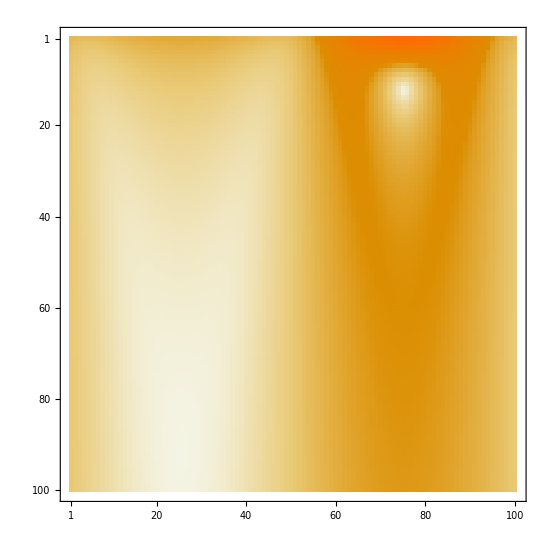

```mathematica
Clear[t]
r=1000; (*m, radius of cylinder*)
a = 9.81; (*m/s^2, radial acceleration at edge of cylinder*)
ω = Sqrt[a/r]; (*rad/s* angular velocity of cylinder*)
Clear[ω,r]
θ =45 Degree;
speed = 30; (*m/s, ball speed*)
earthDist = 67.63; (*m, distance the ball would go on earth*)

posCyl[r_,{x_,y_,z_,q_}]:={r*ArcTan[x/(r-y)],z};
posEarth[ϕ_] := earthDist*{Sin[ϕ],Cos[ϕ]};

RtoS[t_] := { (*change of basis from Rotating to Fixed (standard) reference frame*)
{-Sin[ω*t],-Cos[ω*t],0,r*Cos[ω*t]},
{Cos[ω*t],-Sin[ω*t],0,r*Sin[ω*t]},
{0,0,1,0},
{0,0,0,1}
};

StoR[t_]:=Simplify[Inverse[RtoS[t]]]; (*change of basis matrix from Fixed to Rotating reference frame*)

posRot = {0,1,0,1}; (*initial position in rotating refernce frame*)
vRot = {0,0,0,0}; (*initial velocity in rotating reference frame*)
Clear[vRot]

vAir[{x_,y_,z_,q_}]:=ω{-y,x,0,0}; (*velocity of air in absolute coordinates*)
Cd = 0.3; (*drag coeficient*)
ρ=1.2; (*kg/m^3, density of air*)
A = 0.004; (*m^2, cross sectional area of ball*)
m = 0.145; (*kg* mass of ball*)
ballAirV[p_,v_] := vAir[p]-v; (*airvelocity of ball as function of position and absolute velocity*)
  
dragForce[p_,v_]:=.5*Cd*A*ρ*Norm[ballAirV[p,v]]^2 *ballAirV[p,v]/Norm[ballAirV[p,v]];(*drag force on ball as function of position and absolute velocity*)
dragForce[p_,v_]:={0,0,0,0};
Clear[s]


nRadii = 100;
nAngles = 100;
minRad = 50;
maxRad = 1000;
minAngle = 0 Degree;
maxAngle = 360 Degree;

Zeros[height_,width_]:=Table[0,{i,1,height},{j,1,width}] 
Zeros[size_]:=Zeros[size,size]
cylLocations = Zeros[nRadii,nAngles];
earthLocations = Zeros[nRadii,nAngles];
radii = Array[#&,nRadii,{minRad,maxRad}]//N;
angles = Array[#&,nAngles,{minAngle,maxAngle}]//N;
For[i=1,i≤nRadii,i=i+1,
For[j=1,j≤nAngles,j=j+1,
{
r=radii[[i]],
ϕ=angles[[j]],
ω = Sqrt[a/r],
vRot=speed*{Cos[θ]Sin[ϕ],Sin[θ],Cos[θ]Cos[ϕ],0},
s=NDSolve[
{
m*x''[t]==dragForce[x[t],x'[t]],(*single differential equation*)
x[0]==RtoS[0].posRot,                               (*initial position in fixed frame*)
x'[0]==RtoS'[0].posRot+RtoS[0].vRot,(*initial velocity in fixed frame*)
WhenEvent[Norm[x[t][[{1,2}]]]>=r,{cylLocations[[i,j]]=Evaluate[posCyl[r,StoR[t].x[t]]],earthLocations[[i,j]]=posEarth[ϕ],"StopIntegration"}] (*stop when the ball hits the edge of the cylinder, save the last time and position in end*)
},x,{t,0,1000}
],
rules[[i,j]] = s,
velocities[[i,j]]=Function[t,Evaluate[x'[t]/.rules[[i,j]]]],
paths[[i,j]]=Function[t,Evaluate[Evaluate[StoR[t]].x[t]/.rules[[i,j]]]]
}
]
]
cylLocations//MatrixForm
earthLocations//MatrixForm
MatrixPlot[Map[Norm,earthLocations-cylLocations,{2}]]
```

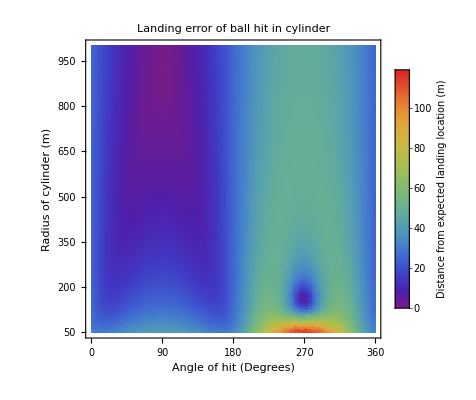

```mathematica
Needs["PlotLegends`"];
errors = Map[Norm,earthLocations-cylLocations,{2}];
ListDensityPlot[errors,ColorFunction->"Rainbow"];
errorsList = Flatten[Table[{angles[[i]]/Degree,radii[[j]],errors[[j,i]]},{i,1,nAngles},{j,1,nRadii}],1];
errorsList2 = Flatten[Table[{(angles[[i]]+2*Pi)/Degree,radii[[j]],errors[[j,i]]},{i,1,nAngles},{j,1,nRadii}],1];
errorsList3 =Flatten[Table[{(angles[[i]]-2*Pi)/Degree,radii[[j]],errors[[j,i]]},{i,1,nAngles},{j,1,nRadii}],1];
errorsListWrap = Join[errorsList,errorsList2,errorsList3];
punchline=ListDensityPlot[errorsList,
ColorFunction->"Rainbow",
PlotLegends->{LegendLabel->Placed["Distance from expected landing location (m)",Right,Rotate[#,90 Degree]&]},
LabelStyle->Directive[Black,Bold,Larger],
PlotLabel->"Landing error of ball hit in cylinder",
FrameLabel->{"Angle of hit (Degrees)","Radius of cylinder (m)"},
FrameTicks->{{0,90,180,270,360}, {50,200,350,500,650,800,950}},
FrameTicks->{{{50,200,350,500,650,800,950},None},{{0,90,180,270,360},None}}]
```